```mathematica
Remove["Global`*"];
```

```mathematica
<<Units`;
```

```mathematica
myunits
```

```mathematica
Second = 100.21; Meter = 1024;
```

## Definitions

```mathematica
(*defintions*)
state = {
leftTilt_,
rightTilt_,
phi_,
phiDot_,
crankRadius_,
biasLF_,
biasLU_,
biasRF_,
biasRU_
};
stateVars = {
leftTilt,
rightTilt,
phi,
phiDot,
crankRadius,
biasLF,
biasLU,
biasRF,
biasRU
};
control = {
leftTiltDot_,
rightTiltDot_
};
controlVars = {
leftTiltDot,
rightTiltDot
};
```

```mathematica
(*time jitter, a jitter, tilt jitter*)
```

```mathematica
processNoise[dtt_, a_, tilt_] = {
tilt/2 dtt^2,
tilt/2 dtt^2,
tilt * dtt^2,
tilt * dtt
};
q[dtt_, a_, tilt_] =
Table[KroneckerDelta[i,j](processNoise[dtt, a, tilt][[i]])^2, {i, 1, 4}, {j, 1, 4}];
qNoise = q[dt, 0.1 Meter/Second^2, 0.1 1/Second^2];
Dimensions[qNoise];
measureNoiseRaw = {0.0882, 0.0882, 0.0882, 0.0882}
measureNoiseUnits = {Meter/Second^2, Meter/Second^2,   Meter/Second^2,  Meter/Second^2};
measureNoise = measureNoiseRaw*measureNoiseUnits;
R =Table[KroneckerDelta[i,j](measureNoiseRaw[[i]]*measureNoiseUnits[[i]])^2, {i, 1, 4}, {j, 1, 4}];
```

{0.0882,0.0882,0.0882,0.0882}

```mathematica
R // MatrixForm
```

((0.00777924 Meter^2)/Second^4 | 0 | 0 | 0
0 | (0.00777924 Meter^2)/Second^4 | 0 | 0
0 | 0 | (0.00777924 Meter^2)/Second^4 | 0
0 | 0 | 0 | (0.00777924 Meter^2)/Second^4)

```mathematica
qNoise//MatrixForm
```

((0.0025 dt^4)/Second^4 | 0 | 0 | 0
0 | (0.0025 dt^4)/Second^4 | 0 | 0
0 | 0 | (0.01 dt^4)/Second^4 | 0
0 | 0 | 0 | (0.01 dt^2)/Second^4)

## Initial Values

```mathematica
(*initial values*)
(*g = 9.8 Meter/Second^2;*)
g = 9.8 Meter/Second^2;
crankRadius = .165 Meter;
initialState = {
1 1,
1 1,
1 1 ,
1 1/Second
};
initialStateErrors = { 
0.1 1,
0.1,
0.11,
0.11/Second
};
initialCovariance = Table[ initialStateErrors[[i]]^2 KroneckerDelta[i,j], {i, Length[initialStateErrors]}, {j,Length[initialStateErrors]}] ;
```

## Predict

```mathematica
(*predict*)
Clear[f]; Clear[F]; Clear[fMatrix];
f[state, control] = {
leftTilt + leftTiltDot*dt,
rightTilt +rightTiltDot*dt,
phi + phiDot*dt ,
phiDot ,
crankRadius,
biasLF,
biasLU,
biasRF,
biasRU
};
(*fMatrix[state, control] = 
FullSimplify[Transpose[
Table[
Derivative[
Table[KroneckerDelta[i,j], {i, Length[state]+Length[control]}]], 
[f][stateVars, controlVars], {j, Length[state]}]]
];*)
fMatrix = D[f[stateVars, controlVars], {stateVars}]
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,dt,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}

```mathematica
fMatrix//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | dt | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
P[oldCovariance_] := fMatrix.oldCovariance.Transpose[fMatrix]+qNoise
```

```mathematica
P[initialCovariance]//MatrixForm
```

(0.01+(0.0025 dt^4)/Second^4 | 0 | 0 | 0
0 | 0.01+(0.0025 dt^4)/Second^4 | 0 | 0
0 | 0 | 0.0121+(0.01 dt^4)/Second^4+(0.0121 dt^2)/Second^2 | (0.0121 dt)/Second^2
0 | 0 | (0.0121 dt)/Second^2 | (0.01 dt^2)/Second^4+0.0121/Second^2)

## Update

```mathematica
(*rotate coord system*)
rotator[ϕ_] = { { Cos[ϕ], Sin[ϕ]}, {-Sin[ϕ], Cos[ϕ]}} ;
(*1% effect, but OK for now*)
(*acceleration in pedal measurement frame*)
pedalPivotAccel[tilt_, Rc_,  θ_, θd_] = (rotator[tilt].Transpose[- Rc θd^2 {{-Cos[θ], -Sin[θ]}} + g{{0, -1}}]);
measureLabels = { lAF, lAU, rAF, rAU, lG, rG };
pedalPivotAccel[0, 0.165Meter, 0, 70 * (2π)/(60 Second)][[1]][[1]] Second^2/Meter;
```

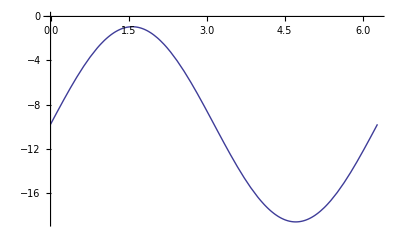

```mathematica
Plot[pedalPivotAccel[0, 0.165 Meter, x , 70 * 2 π/(60 Second)][[2]][[1]] Second^2/Meter, {x, 0, 2π}]
```

```mathematica
h[state] = {
(*laf*)pedalPivotAccel[leftTilt,crankRadius, phi,phiDot][[1]][[1]] + biasLF,
(*lau*)pedalPivotAccel[leftTilt,crankRadius, phi,phiDot][[2]][[1]] + biasLU,
(*raf*)pedalPivotAccel[rightTilt,crankRadius,phi+π ,phiDot][[1]][[1]] + biasRF,
(*rau*)pedalPivotAccel[rightTilt,crankRadius,phi +π,phiDot][[2]][[1]] + biasRU
};
hMatrix[state] = 
FullSimplify[Transpose[
Table[
Derivative[
Table[KroneckerDelta[i,j], {i, Length[state]}]]
[h][stateVars], {j, Length[state]}]
]];
```

```mathematica
FullSimplify[h[stateVars]] // MatrixForm
```

(biasLF+crankRadius phiDot^2 Cos[leftTilt-phi]-g Sin[leftTilt]
biasLU-g Cos[leftTilt]-crankRadius phiDot^2 Sin[leftTilt-phi]
biasRF-crankRadius phiDot^2 Cos[phi-rightTilt]-g Sin[rightTilt]
biasRU-g Cos[rightTilt]-crankRadius phiDot^2 Sin[phi-rightTilt])

```mathematica
testCov = {{aa, bb}, {cc, dd}};
testH = {{a, b}};
```

```mathematica
testH//MatrixForm
```

(a | b)

```mathematica
testH.testCov.Transpose[testH] // MatrixForm
```

(a (a aa+b cc)+b (a bb+b dd))

```mathematica
{a, b}.{{aa, bb}, {{
```

```mathematica
hMatrix[stateVars]  // MatrixForm
```

(-g Cos[leftTilt]-crankRadius phiDot^2 Sin[leftTilt-phi] | 0 | crankRadius phiDot^2 Sin[leftTilt-phi] | 2 crankRadius phiDot Cos[leftTilt-phi] | phiDot^2 Cos[leftTilt-phi] | 1 | 0 | 0 | 0
-crankRadius phiDot^2 Cos[leftTilt-phi]+g Sin[leftTilt] | 0 | crankRadius phiDot^2 Cos[leftTilt-phi] | -2 crankRadius phiDot Sin[leftTilt-phi] | -phiDot^2 Sin[leftTilt-phi] | 0 | 1 | 0 | 0
0 | -g Cos[rightTilt]-crankRadius phiDot^2 Sin[phi-rightTilt] | crankRadius phiDot^2 Sin[phi-rightTilt] | -2 crankRadius phiDot Cos[phi-rightTilt] | -phiDot^2 Cos[phi-rightTilt] | 0 | 0 | 1 | 0
0 | crankRadius phiDot^2 Cos[phi-rightTilt]+g Sin[rightTilt] | -crankRadius phiDot^2 Cos[phi-rightTilt] | -2 crankRadius phiDot Sin[phi-rightTilt] | -phiDot^2 Sin[phi-rightTilt] | 0 | 0 | 0 | 1)

```mathematica
({{-g Cos[leftTilt]-crankRadius phiDot^2 Sin[leftTilt-phi], 0, crankRadius phiDot^2 Sin[leftTilt-phi], 2 crankRadius phiDot Cos[leftTilt-phi], phiDot^2 Cos[leftTilt-phi], 1, 0, 0, 0}, {-crankRadius phiDot^2 Cos[leftTilt-phi]+g Sin[leftTilt], 0kkkkj, crankRadius phiDot^2 Cos[leftTilt-phi], -2 crankRadius phiDot Sin[leftTilt-phi], -phiDot^2 Sin[leftTilt-phi], 0, 1, 0, 0}, {0, -g Cos[rightTilt]-crankRadius phiDot^2 Sin[phi-rightTilt], crankRadius phiDot^2 Sin[phi-rightTilt], -2 crankRadius phiDot Cos[phi-rightTilt], -phiDot^2 Cos[phi-rightTilt], 0, 0, 1, 0}, {0, crankRadius phiDot^2 Cos[phi-rightTilt]+g Sin[rightTilt], -crankRadius phiDot^2 Cos[phi-rightTilt], -2 crankRadius phiDot Sin[phi-rightTilt], -phiDot^2 Sin[phi-rightTilt], 0, 0, 0, 1}})
```

```mathematica
hMatrix[stateVars][[All,5]] // MatrixForm
```

(phiDot^2 Cos[leftTilt-phi]
-phiDot^2 Sin[leftTilt-phi]
-phiDot^2 Cos[phi-rightTilt]
-phiDot^2 Sin[phi-rightTilt])

```mathematica
y[measure_, stater_] := measure - h[stater];
```

```mathematica
S[stater_, oldCovariance_] := hMatrix[stater].oldCovariance.Transpose[hMatrix[stater]] + R
```

```mathematica
S[initialState, initialCovariance] // MatrixForm
```

((0.289463 Meter^2)/Second^4 | -(0.427908 Meter^2)/Second^4 | -(0.00131769 Meter^2)/Second^4 | (0. Meter^2)/Second^4
-(0.427908 Meter^2)/Second^4 | (0.661201 Meter^2)/Second^4 | (0. Meter^2)/Second^4 | -(0.000329423 Meter^2)/Second^4
-(0.00131769 Meter^2)/Second^4 | (0. Meter^2)/Second^4 | (0.289463 Meter^2)/Second^4 | -(0.445381 Meter^2)/Second^4
(0. Meter^2)/Second^4 | -(0.000329423 Meter^2)/Second^4 | -(0.445381 Meter^2)/Second^4 | (0.715628 Meter^2)/Second^4)

```mathematica
Dimensions[S[initialState, initialCovariance] ]
```

{4,4}

```mathematica
K [stater_, oldCovariance_] := oldCovariance.Transpose[hMatrix[stater]].Inverse[S[stater, oldCovariance]];
```

```mathematica
Simplify[K[initialState, initialCovariance]] // MatrixForm
```

(-(0.0522799 Second^2)/Meter | (0.0883881 Second^2)/Meter | -(0.00413626 Second^2)/Meter | -(0.00253358 Second^2)/Meter
-(0.00370743 Second^2)/Meter | -(0.00235606 Second^2)/Meter | -(0.0493194 Second^2)/Meter | (0.0868433 Second^2)/Meter
(0.0925865 Second^2)/Meter | (0.0629091 Second^2)/Meter | -(0.0902459 Second^2)/Meter | -(0.0589268 Second^2)/Meter
(0.284796 Second)/Meter | (0.18422 Second)/Meter | -(0.291677 Second)/Meter | -(0.181444 Second)/Meter)

```mathematica
xNew[stater_,  oldCovariance_, measure_] := stater + K[stater, oldCovariance].y[measure,stater];
```

```mathematica
xNew[initialState, initialCovariance, measureNoise] //N
```

{0.780968,0.78309,0.835072,0.482971/Second}

```mathematica
(*pNew[stater_,  oldCovariance_] := (IdentityMatrix[Length[state]]-(K[stater, P[ oldCovariance]].hMatrix[stater])).P[ oldCovariance].Transpose[(IdentityMatrix[Length[state]]-(K[stater, P[ oldCovariance]].hMatrix[stater]))]+K[stater, P[ oldCovariance]].R.Transpose[K[stater, P[ oldCovariance]]];*)
```

```mathematica
pNew[stater_, oldCovariance_] :=
(IdentityMatrix[Length[state]] - K[stater, P[oldCovariance]].hMatrix[stater]).P[oldCovariance];
```

```mathematica
Simplify[K[initialState, P[initialCovariance]]]// MatrixForm
```

((0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(9.04032×10^-25 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0000332262 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000130809 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000430639 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(9.93802×10^-6 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000104771 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000671449 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(4.34378×10^-24 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000133398 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000144192 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000146312 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(9.93802×10^-6 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000011639 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0000945276 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4)
(0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(1.51746×10^-24 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000144665 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000017344 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000144061 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(8.26093×10^-6 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(8.06659×10^-6 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0000909515 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(4.38745×10^-24 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0000309783 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000124387 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000421543 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(8.26093×10^-6 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000989564 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000656584 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4)
(0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^8)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(2.11388×10^-25 dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(4.23516×10^-22 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00118242 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00364547 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00687398 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^8)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000713137 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00222174 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00467774 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^8)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(3.30872×10^-22 dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00111629 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00352363 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0071617 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^8)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^4 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000778756 dt^2 Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0023446 dt Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00438858 Second^5)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4)
(0. dt^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(9.66898×10^-24 dt^3 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(9.65×10^-6 dt^2 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00110236 dt Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0094205 Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^5)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000134547 dt^2 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.000775828 dt Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.00611649 Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^5)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.0000174229 dt^2 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00117734 dt Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00951153 Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^5)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4) | (0. dt^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^7)/(Meter Second^3 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^6)/(Meter Second^2 (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^3 Second)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0.0000134547 dt^2 Second^2)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.000700519 dt Second^3)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))-(0.00602592 Second^4)/(Meter (2.64698×10^-23 dt^3+0.000246162 dt^2 Second+0.00151202 dt Second^2+0.00773495 Second^3))+(0. dt^5)/(2.64698×10^-23 dt^3 Meter Second+0.000246162 dt^2 Meter Second^2+0.00151202 dt Meter Second^3+0.00773495 Meter Second^4))

```mathematica
pNew[initialState, initialCovariance] // MatrixForm
```

(«1»)

```mathematica
Dimensions[%]
```

{4,4}

```mathematica
Convert[70 *2Pi Radian/Minute, Radian/Second]
```

(7 π Radian)/(3 Second)

```mathematica
finalRate = 150 * 2 π/(60 Second); (*70 RPM*) riseTime = 4 Second; gearRatio = 5; wheelRadius = 0.7 Meter; trueCrank = .165 Meter; maxPedalTilt = 0.1(*(10/360)2π *); (*10 degree*)stopTime=1Second;
truthPedalPhi[t_] = finalRate*t/(1+ t/stopTime)*(1-Exp[-((t/riseTime)^2)]);
truthPedalPhiDot[t_] = D[truthPedalPhi[t], t];
truthPedalPhiAcc[t_] = D[truthPedalPhi[t], {t,2}];
truthAccel[t_] = truthPedalPhiAcc[t]*gearRatio*wheelRadius;
pedalTiltFunction[phi_] = maxPedalTilt*Sin[phi]+ maxPedalTilt/2;
truthLeftTilt[t_] = pedalTiltFunction[truthPedalPhi[t]];
truthRightTilt[t_] = pedalTiltFunction[truthPedalPhi[t]+π];
truthLeftTiltDot[t_] = D[truthLeftTilt[t], t];
truthRightTiltDot[t_] = D[truthRightTilt[t], t];
trueState[t_] = 
{
truthLeftTilt[t],
truthRightTilt[t],
truthPedalPhi[t],
truthPedalPhiDot[t]
};
Clear[shootMeasurementNoise]; Clear[noisyMeasurements]; Clear[noisyControl];
noisyControl[t_] := noisyControl[t]= {truthLeftTiltDot[t] + RandomReal[NormalDistribution[0, 0.05]]/Second, truthRightTiltDot[t] + RandomReal[NormalDistribution[0, 0.05]]/Second};

shootMeasurementNoise[t_] := shootMeasurementNoise[t]= Table[RandomReal[NormalDistribution[0,measureNoiseRaw[[x]]]], {x, Length[measureNoiseRaw]}]*measureNoiseUnits;
shootMeasurementNoise[10]
noisyMeasurements[t_] := noisyMeasurements[t]= h[trueState[t]] +shootMeasurementNoise[t];
```

{(0.0453542 Meter)/Second^2,(0.0995137 Meter)/Second^2,-(0.0853852 Meter)/Second^2,-(0.0243571 Meter)/Second^2}

```mathematica
?truthPedalPhi
```

```mathematica
trueState[1 Second][[3]]
```

7/3 (1-1/ⅇ^(1/16)) π

```mathematica
UnitStep[1 ]
```

1

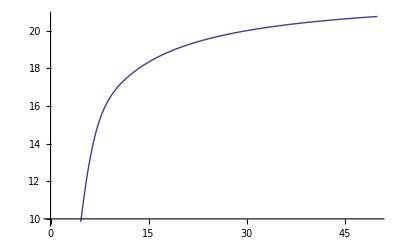

```mathematica
Plot[trueState[t Second][[3]], {t, 0, 50}]
```

```mathematica
(noisyMeasurements[1000 Second]-h[trueState[1000 Second]])/h[trueState[1000 Second]] // N
```

{0.,0.,0.,0.}

```mathematica
dt = 0.01 Second;
startTime = 0.5 Second;
ClearAll[kalmanState]; ClearAll[kalmanCovariance]; ClearAll[difference]
kalmanState[0] = trueState[startTime] // N;
kalmanCovariance[0] =  1*initialCovariance;
kalmanState[n_] :=  kalmanState[n] =
 f[kalmanState[n-1], noisyControl[startTime + n*dt]]+K[kalmanState[n-1], P[ kalmanCovariance[n-1]] ].y[noisyMeasurements[n*dt+startTime], f[kalmanState[n-1], noisyControl[startTime+n*dt]]];
kalmanCovariance[n_] := kalmanCovariance[n] = pNew[ kalmanState[n-1], kalmanCovariance[n-1]];
difference[n_] := (kalmanState[n]-trueState[startTime + n*dt])(*/trueState[startTime+n*dt]*)// MatrixForm
tester[n_] := {difference[n] //MatrixForm// N,
trueState[startTime+n*dt] // MatrixForm}
```

```mathematica
tester[100]
```

{(0.00751364
-0.0141086
-0.163986
-0.150643/Second),(0.14446
-0.0444605
1.23639
1.86503/Second)}

```mathematica
kalmanState[2][[3]]
```

0.0671651

```mathematica
testPosition[y_, index_, multiple_] := ListLinePlot[{Table[trueState[startTime+n*dt][[index]]*multiple, {n, 0, y}], Table[kalmanState[n][[index]]*multiple, {n, 0, y}]}, InterpolationOrder->2]
```

```mathematica
testErrors[y_, index_, multiple_] := ListLinePlot[Table[trueState[startTime+n*dt][[index]]*multiple, {n, 0, y}]- Table[kalmanState[n][[index]]*multiple, {n, 0, y}], InterpolationOrder->2]
```

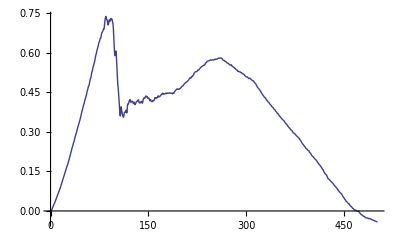

```mathematica
testErrors[500, 4, Second]
```

```mathematica
validate[y_] :={testPosition[y, 1, 1], testPosition[y, 2, 1],testPosition[y, 3, 1/π], testPosition[y, 4, Second]}
```

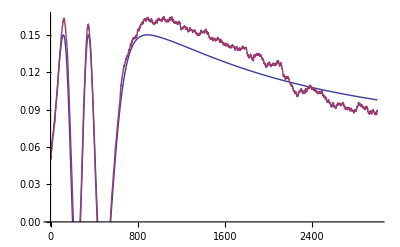
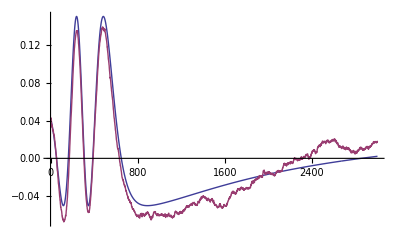
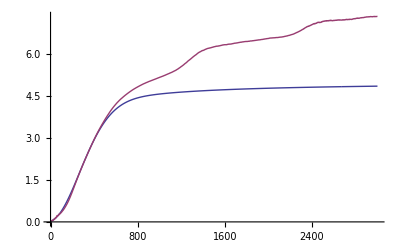
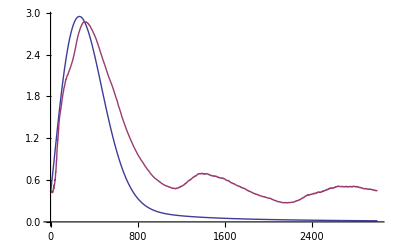

```mathematica
validate[3000]
```